This calculation is for a two plaquette system with periodic boundary conditions and mirroring between the upper and lower links on a matterless lattice. Using Soni and Trivedi’s definition of entanglement entropy, the entanglement entropy is calculated for an SU(3) gauge theory with truncation at the 3 and 3 bar representations. This notebook extends the calculation to the first excited state, and then calculates a hypothetical “entanglement temperature” based on the change in entropy.

To begin, we need to determine the first excited state. This is done by considering the second-lowest energy eigenstate of the Hamiltonian. There are degeneracies for the excited states as the magnetic terms begin to dominate, since there are a lot of symmetries that are only broken once the electric terms come into play.

```mathematica
k1:={{1},{0},{0}}
k3:={{0},{1},{0}}
k3b:={{0},{0},{1}}
k111:=KroneckerProduct[KroneckerProduct[k1,k1],k1]
k13b1:=KroneckerProduct[KroneckerProduct[k1,k3b],k1]
k131:=KroneckerProduct[KroneckerProduct[k1,k3],k1]
k33b3:=KroneckerProduct[KroneckerProduct[k3,k3b],k3]
k3b33b:=KroneckerProduct[KroneckerProduct[k3b,k3],k3b]
k313:=KroneckerProduct[KroneckerProduct[k3b,k1],k3b]
k3b13b:=KroneckerProduct[KroneckerProduct[k3,k1],k3]
k333:=KroneckerProduct[KroneckerProduct[k3,k3],k3]
k3b3b3b:=KroneckerProduct[KroneckerProduct[k3b,k3b],k3b]
k311:=KroneckerProduct[KroneckerProduct[k3,k1],k1]
k3b11:=KroneckerProduct[KroneckerProduct[k3b,k1],k1]
k133:=KroneckerProduct[KroneckerProduct[k1,k3],k3]
k13b3b:=KroneckerProduct[KroneckerProduct[k1,k3b],k3b]
k33b3b:=KroneckerProduct[KroneckerProduct[k3,k3b],k3b]
k3b33:=KroneckerProduct[KroneckerProduct[k3b,k3],k3]
Hb33[g_,a_]:=1/(2g^2a^2){{6,0,0,-1,-1,-1,-1,0,0},{0,6,0,-1,0,-1,0,-1,-1},{0,0,6,0,-1,0,-1,-1,-1},{-1,-1,0,6,-1,0,0,0,-1},{-1,0,-1,-1,6,0,0,-1,0},{-1,-1,0,0,0,6,-1,-1,0},{-1,0,-1,0,0,-1,6,0,-1},{0,-1,-1,0,-1,-1,0,6,0},{0,-1,-1,-1,0,0,-1,0,6}}
He33[g_]:=g^2/2{{0,0,0,0,0,0,0,0,0},{0,16/3,0,0,0,0,0,0,0},{0,0,16/3,0,0,0,0,0,0},{0,0,0,16/3,0,0,0,0,0},{0,0,0,0,16/3,0,0,0,0},{0,0,0,0,0,16/3,0,0,0},{0,0,0,0,0,0,16/3,0,0},{0,0,0,0,0,0,0,8,0},{0,0,0,0,0,0,0,0,8}}
H33[g_,a_]:=He33[g]+Hb33[g,a]+500IdentityMatrix[9]
```

```mathematica
Manipulate[Eigenvalues[H33[g,1]-500IdentityMatrix[9]],{g,Sqrt[0.0001],0.9}]
```

For the purposes of this calculation, we’ll restrict g to be greater than 0.1, so that degeneracies don’t matter. Now we can compute the eigenstate. Here, we actually calculate the nth state (note that because of the way Mathematica works, these are actually in reverse order, so that state 1 is at the energy cutoff, while state 9 is the ground state), so that we can just reuse this code for other stuff if we need to.

```mathematica
StateN33[g_,a_,n_]:=Part[Eigenvectors[H33[g,a]],n]
e1[g_,a_,n_]:=Part[StateN33[g,a,n],1]k111
e2[g_,a_,n_]:=Part[StateN33[g,a,n],2]k13b1
e3[g_,a_,n_]:=Part[StateN33[g,a,n],3]k131
e4[g_,a_,n_]:=Part[StateN33[g,a,n],4]k33b3
e5[g_,a_,n_]:=Part[StateN33[g,a,n],5]k3b33b
e6[g_,a_,n_]:=Part[StateN33[g,a,n],6]k3b13b
e7[g_,a_,n_]:=Part[StateN33[g,a,n],7]k313
e8[g_,a_,n_]:=Part[StateN33[g,a,n],8]k333
e9[g_,a_,n_]:=Part[StateN33[g,a,n],9]k3b3b3b
f1[g_,a_,n_]:=Part[StateN33[g,a,n],1]k111
f2[g_,a_,n_]:=Part[StateN33[g,a,n],2]k311
f3[g_,a_,n_]:=Part[StateN33[g,a,n],3]k3b11
f4[g_,a_,n_]:=Part[StateN33[g,a,n],4]k133
f5[g_,a_,n_]:=Part[StateN33[g,a,n],5]k13b3b
f6[g_,a_,n_]:=Part[StateN33[g,a,n],6]k33b3b
f7[g_,a_,n_]:=Part[StateN33[g,a,n],7]k3b33
f8[g_,a_,n_]:=Part[StateN33[g,a,n],8]k333
f9[g_,a_,n_]:=Part[StateN33[g,a,n],9]k3b3b3b
```

```mathematica
RDM33A[g_,a_,n_]:=
e1[g,a,n].Transpose[e1[g,a,n]]+e1[g,a,n].Transpose[e4[g,a,n]]+e1[g,a,n].Transpose[e5[g,a,n]]+
e2[g,a,n].Transpose[e2[g,a,n]]+e2[g,a,n].Transpose[e6[g,a,n]]+e2[g,a,n].Transpose[e8[g,a,n]]+
e3[g,a,n].Transpose[e3[g,a,n]]+e3[g,a,n].Transpose[e7[g,a,n]]+e3[g,a,n].Transpose[e9[g,a,n]]+
e4[g,a,n].Transpose[e1[g,a,n]]+e4[g,a,n].Transpose[e4[g,a,n]]+e4[g,a,n].Transpose[e5[g,a,n]]+
e5[g,a,n].Transpose[e1[g,a,n]]+e5[g,a,n].Transpose[e4[g,a,n]]+e5[g,a,n].Transpose[e5[g,a,n]]+
e6[g,a,n].Transpose[e2[g,a,n]]+e6[g,a,n].Transpose[e6[g,a,n]]+e6[g,a,n].Transpose[e8[g,a,n]]+
e7[g,a,n].Transpose[e3[g,a,n]]+e7[g,a,n].Transpose[e7[g,a,n]]+e7[g,a,n].Transpose[e9[g,a,n]]+
e8[g,a,n].Transpose[e2[g,a,n]]+e8[g,a,n].Transpose[e6[g,a,n]]+e8[g,a,n].Transpose[e8[g,a,n]]+
e9[g,a,n].Transpose[e3[g,a,n]]+e9[g,a,n].Transpose[e7[g,a,n]]+e9[g,a,n].Transpose[e9[g,a,n]]
RDM33B[g_,a_,n_]:=
f1[g,a,n].Transpose[f1[g,a,n]]+f1[g,a,n].Transpose[f4[g,a,n]]+f1[g,a,n].Transpose[f5[g,a,n]]+
f2[g,a,n].Transpose[f2[g,a,n]]+f2[g,a,n].Transpose[f6[g,a,n]]+f2[g,a,n].Transpose[f8[g,a,n]]+
f3[g,a,n].Transpose[f3[g,a,n]]+f3[g,a,n].Transpose[f7[g,a,n]]+f3[g,a,n].Transpose[f9[g,a,n]]+
f4[g,a,n].Transpose[f1[g,a,n]]+f4[g,a,n].Transpose[f4[g,a,n]]+f4[g,a,n].Transpose[f5[g,a,n]]+
f5[g,a,n].Transpose[f1[g,a,n]]+f5[g,a,n].Transpose[f4[g,a,n]]+f5[g,a,n].Transpose[f5[g,a,n]]+
f6[g,a,n].Transpose[f2[g,a,n]]+f6[g,a,n].Transpose[f6[g,a,n]]+f6[g,a,n].Transpose[f8[g,a,n]]+
f7[g,a,n].Transpose[f3[g,a,n]]+f7[g,a,n].Transpose[f7[g,a,n]]+f7[g,a,n].Transpose[f9[g,a,n]]+
f8[g,a,n].Transpose[f2[g,a,n]]+f8[g,a,n].Transpose[f6[g,a,n]]+f8[g,a,n].Transpose[f8[g,a,n]]+
f9[g,a,n].Transpose[f3[g,a,n]]+f9[g,a,n].Transpose[f7[g,a,n]]+f9[g,a,n].Transpose[f9[g,a,n]]
```

Now for the temperature. Firstly, we can check the entanglement entropies for say, the ground state and the first excited state. This is relatively computationally expensive:

```mathematica
S33A[g_,a_,n_]:=-Part[Eigenvalues[RDM33A[g,a,n]],1]Log[Part[Eigenvalues[RDM33A[g,a,n]],1]]-Part[Eigenvalues[RDM33A[g,a,n]],2]Log[Part[Eigenvalues[RDM33A[g,a,n]],2]]-Part[Eigenvalues[RDM33A[g,a,n]],3]Log[Part[Eigenvalues[RDM33A[g,a,n]],3]]
S33B[g_,a_,n_]:=-Part[Eigenvalues[RDM33B[g,a,n]],1]Log[Part[Eigenvalues[RDM33B[g,a,n]],1]]-Part[Eigenvalues[RDM33B[g,a,n]],2]Log[Part[Eigenvalues[RDM33B[g,a,n]],2]]-Part[Eigenvalues[RDM33B[g,a,n]],3]Log[Part[Eigenvalues[RDM33B[g,a,n]],3]]
```

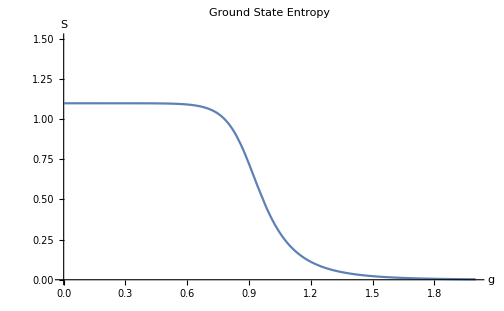

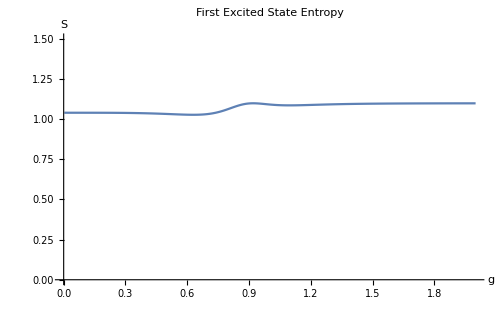

```mathematica
Plot[S33A[g,1,9],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"Ground State Entropy",PlotRange->{{0,2},{0,1.5}}]
Plot[S33A[g,1,8],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"First Excited State Entropy",PlotRange->{{0,2},{0,1.5}}]
```

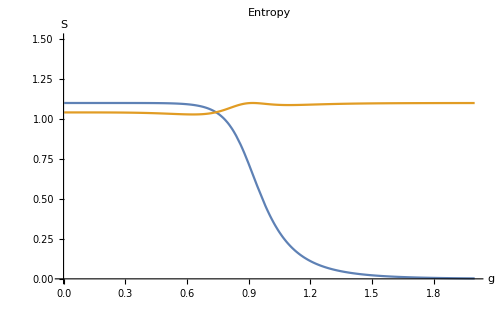

```mathematica
Plot[{S33A[g,1,9],S33A[g,1,8]},{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"Entropy",PlotRange->{{0,2},{0,1.5}}]
```

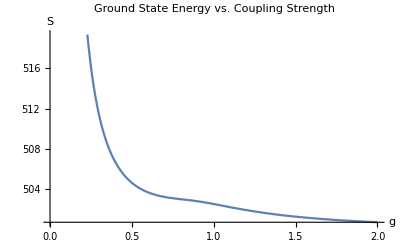

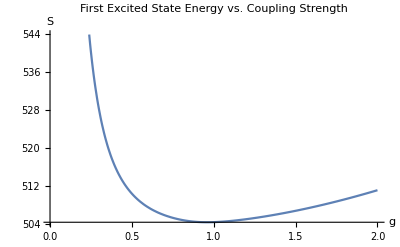

```mathematica
Plot[Part[Eigenvalues[H33[g,1]],9],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"Ground State Energy vs. Coupling Strength"]
Plot[Part[Eigenvalues[H33[g,1]],8],{g,Sqrt[0.00001],2},AxesLabel->{"g","S"},PlotLabel->"First Excited State Energy vs. Coupling Strength"]
```

And of course we can check to see if the first excited state is behaving appropriately as well:

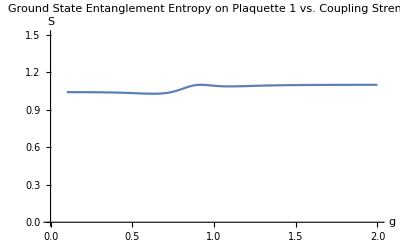

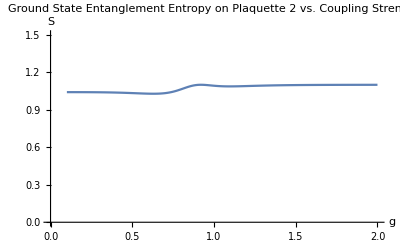

```mathematica
Plot[S33A[g,1,8],{g,0.1,2},AxesLabel->{"g","S"},PlotLabel->"Ground State Entanglement Entropy on Plaquette 1 vs. Coupling Strength",PlotRange->{{0,2},{0,1.5}}]
Plot[S33B[g,1,8],{g,0.1,2},AxesLabel->{"g","S"},PlotLabel->"Ground State Entanglement Entropy on Plaquette 2 vs. Coupling Strength",PlotRange->{{0,2},{0,1.5}}]
```

Interestingly, the entanglement entropies on the first excited state seem to be essentially constant, with a slight bump in the phase transition where the magnetic and electric terms are of equal strength. Also, the first excited state is slightly less entangled than the ground state for low g (magnetic terms dominating -- why? 

Let’s define the entanglement temperature as  and see what we get:

```mathematica
EntanglementTemperature[g_,a_,n_]:=1/((S33A[g,a,n]-S33A[g,a,n+1])/(Part[Eigenvalues[H33[g,a]],n]-Part[Eigenvalues[H33[g,a]],n+1]))
```

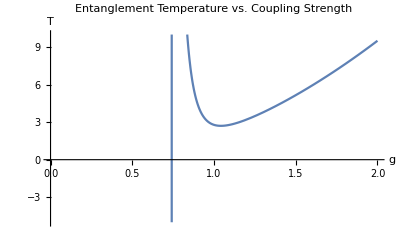

```mathematica
Plot[EntanglementTemperature[g,1,8],{g,0.1,2},AxesLabel->{"g","T"},PlotLabel->"Entanglement Temperature vs. Coupling Strength",PlotRange->{{0,2},{-5,10}}]
```

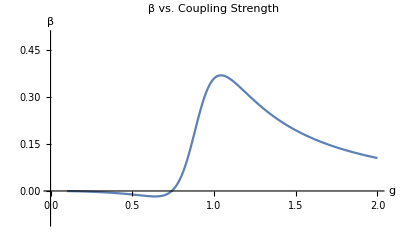

```mathematica
Plot[1/EntanglementTemperature[g,1,8],{g,0.1,2},AxesLabel->{"g","β"},PlotLabel->"β vs. Coupling Strength",PlotRange->{{0,2},{-0.1,0.5}}]
```

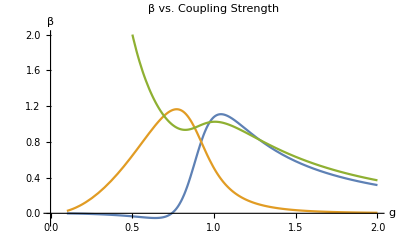

```mathematica
Plot[{3/EntanglementTemperature[g,1,8],Transpose[StateN33[g,1,9]].He33[g].StateN33[g,1,9],Transpose[StateN33[g,1,9]].Hb33[g,1].StateN33[g,1,9]/2},{g,0.1,2},AxesLabel->{"g","β"},PlotLabel->"β vs. Coupling Strength",PlotRange->{{0,2},{-0.1,2}}]
```

So I need to think of an interpretation for entanglement temperature. Thermodynamically, it’s an expression of a system’s desire to maximize the number of microstates available to it. If a small change in energy results in a huge change in entropy, we’re at very low temperature; if a large change in energy results in a tiny change in entropy, we’re at a very high temperature. In this case, what we can first notice is that below a particular coupling strength (g~0.75, about the start of the phase transition), the first excited state actually represents a decrease in entanglement entropy. (Interpretation?) Entropy can decrease locally if it dumps the entropy elsewhere, assuming entanglement entropy is like regular entropy.

```mathematica
EntropyData := Table[{g,S33A[g,1,9]},{g,Range[0.1,2,0.001]}]
```

```mathematica
FindFit[EntropyData, a Tanh[b g + c]+d,{{a,0.1},{b,-4},{c,3.6},{d,1}},g]
```

{a→0.543413,b→-5.68307,c→5.43197,d→0.563084}

```mathematica
EntropyFunction[g_]:=0.543413Tanh[-5.68307g+5.43197]+0.563084
```

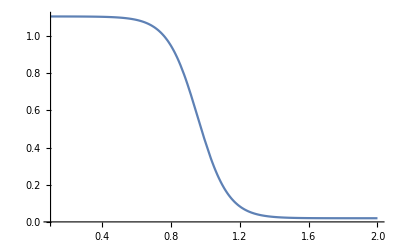

```mathematica
Plot[EntropyFunction[g],{g,0.1,2}]
```

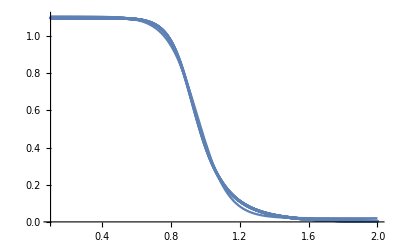

```mathematica
Show[Plot[EntropyFunction[g],{g,0.1,2}],ListPlot[EntropyData,PlotRange->All]]
```

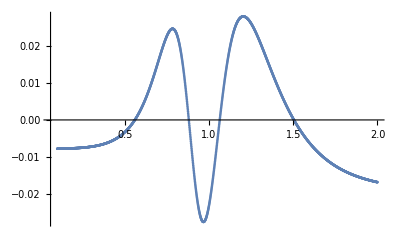

```mathematica
residuals:=Apply[Function[{t,y},Evaluate[{t,y-EntropyFunction[t]}]],EntropyData,1]
ListPlot[residuals,PlotRange->All]
```

```mathematica
D[EntropyFunction[g],g]
```

-3.08825 Sech[5.43197-5.68307 g]^2

```mathematica
EntropyDerivative[g_]:=-3.08825411791 Sech[5.43197-5.68307 g]^2
```

```mathematica
EnergyDerivative[g_]=D[Part[Eigenvalues[H33[g,1]],9],g]
```

-1/(3 g^3)Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]+(-98496000 g-60264953856 g^3-11178852768000 g^5-648209090377728 g^7-15121071360000 g^9-110593327104 g^11-258048000 g^13-(-20088000 g-7452189504 g^3-648104544000 g^5-12096285696 g^7-61440000 g^9-73728 g^11) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]-(1242000 g+216011616 g^3+3024000 g^5+8192 g^7) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^2-(-24000 g-224 g^3) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^3)/(6 g^2 (-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12+2 (1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]+3 (-69-12000 g^2-56 g^4) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^2+4 Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^3))

```mathematica
EnergyDerivative[g_]:=-1/(3 g^3)Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]+(-98496000 g-60264953856 g^3-11178852768000 g^5-648209090377728 g^7-15121071360000 g^9-110593327104 g^11-258048000 g^13-(-20088000 g-7452189504 g^3-648104544000 g^5-12096285696 g^7-61440000 g^9-73728 g^11) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]-(1242000 g+216011616 g^3+3024000 g^5+8192 g^7) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^2-(-24000 g-224 g^3) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^3)/(6 g^2 (-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12+2 (1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]+3 (-69-12000 g^2-56 g^4) Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^2+4 Root[51840+49248000 g^2+15066238464 g^4+1863142128000 g^6+81026136297216 g^8+1512107136000 g^10+9216110592 g^12+18432000 g^14+(-16416-10044000 g^2-1863047376 g^4-108017424000 g^6-1512035712 g^8-6144000 g^10-6144 g^12) #1+(1674+621000 g^2+54002904 g^4+504000 g^6+1024 g^8) #1^2+(-69-12000 g^2-56 g^4) #1^3+#1^4&,4]^3))
```

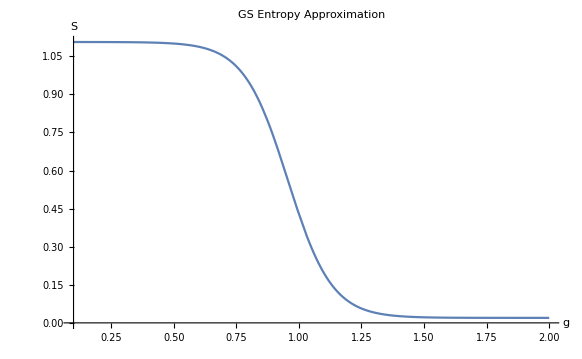

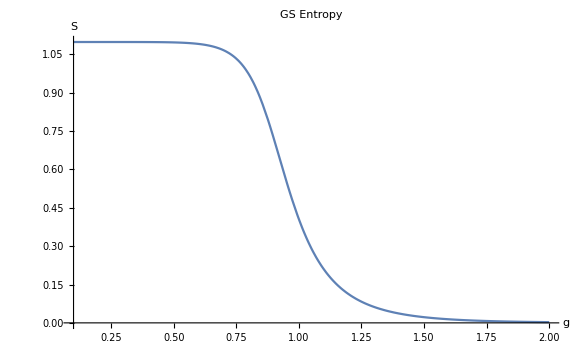

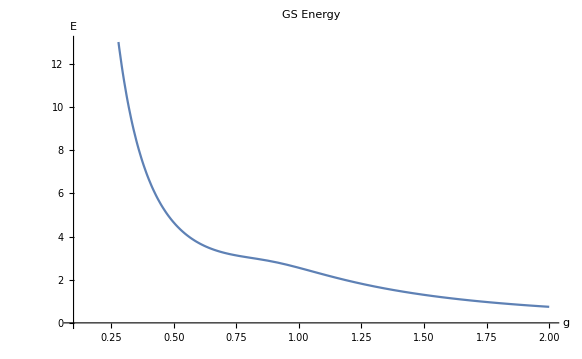

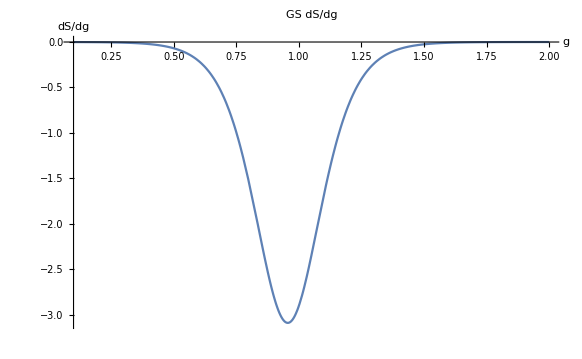

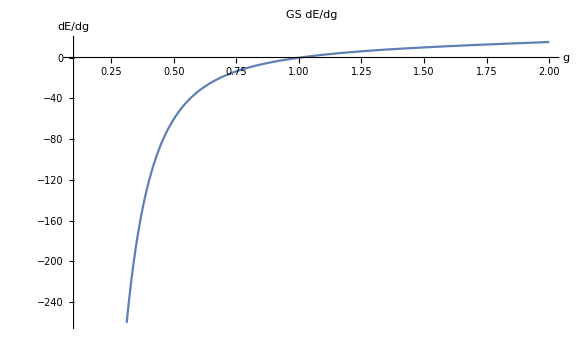

```mathematica
Plot[EntropyFunction[g],{g,0.1,2},PlotLabel->"GS Entropy Approximation",AxesLabel->{"g","S"}]
Plot[S33A[g,1,9],{g,0.1,2},PlotLabel->"GS Entropy",AxesLabel->{"g","S"}]
Plot[Part[Eigenvalues[H33[g,1]-500IdentityMatrix[9]],9],{g,0.1,2},PlotLabel->"GS Energy",AxesLabel->{"g","E"}]
Plot[EntropyDerivative[g],{g,0.1,2},PlotLabel->"GS dS/dg",AxesLabel->{"g","dS/dg"}]
Plot[EnergyDerivative[g],{g,0.1,2},PlotLabel->"GS dE/dg",AxesLabel->{"g","dE/dg"}]
```

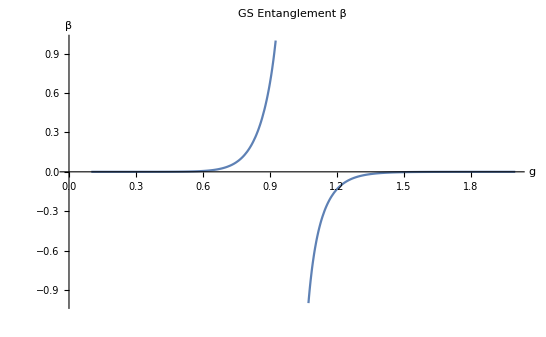

```mathematica
Plot[EntropyDerivative[g]/EnergyDerivative[g],{g,0.1,2},PlotRange->{{0,2},{-1,1}},PlotLabel->"GS Entanglement β",AxesLabel->{"g","β"}]
```

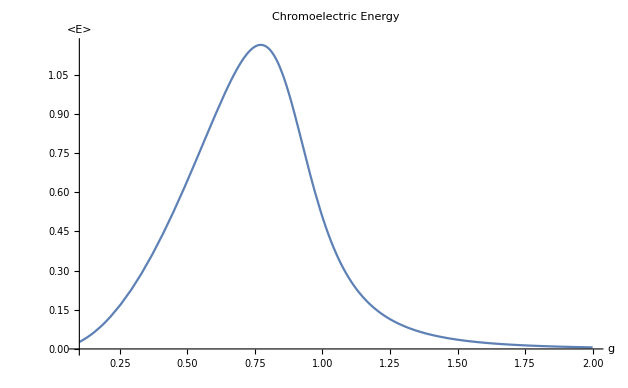

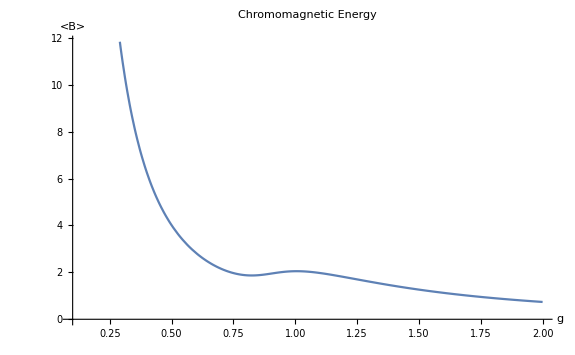

```mathematica
Plot[Transpose[StateN33[g,1,9]].He33[g].StateN33[g,1,9],{g,0.1,2},PlotLabel->"Chromoelectric Energy",AxesLabel->{"g","<E>"}]
Plot[Transpose[StateN33[g,1,9]].Hb33[g,1].StateN33[g,1,9],{g,0.1,2},PlotLabel->"Chromomagnetic Energy",AxesLabel->{"g","<B>"}]
```

```mathematica
EntanglementBeta[g_]:=EntropyDerivative[g]/EnergyDerivative[g]
```

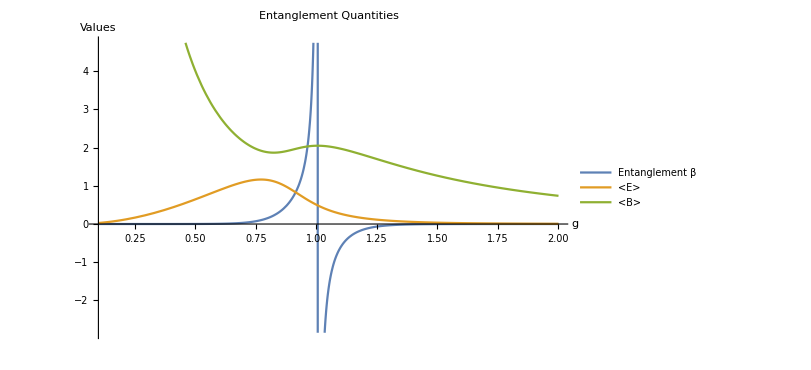

```mathematica
Plot[{EntanglementBeta[g],Transpose[StateN33[g,1,9]].He33[g].StateN33[g,1,9],Transpose[StateN33[g,1,9]].Hb33[g,1].StateN33[g,1,9]},{g,0.1,2},PlotLabel->"Entanglement Quantities",AxesLabel->{"g","Values"},PlotLegends->LineLegend[{"Entanglement β","<E>","<B>"}]]
```

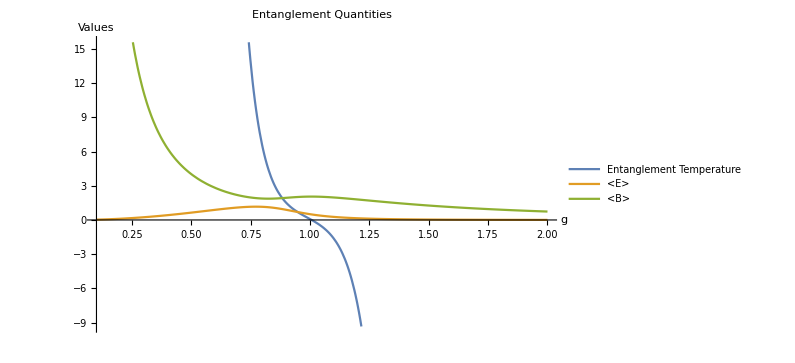

```mathematica
Plot[{1/EntanglementBeta[g],Transpose[StateN33[g,1,9]].He33[g].StateN33[g,1,9],Transpose[StateN33[g,1,9]].Hb33[g,1].StateN33[g,1,9]},{g,0.1,2},PlotLabel->"Entanglement Quantities",AxesLabel->{"g","Values"},PlotLegends->LineLegend[{"Entanglement Temperature","<E>","<B>"}]]
```

```mathematica
EntropyData1E := Table[{g,S33A[g,1,8]},{g,Range[0.1,2,0.001]}]
```

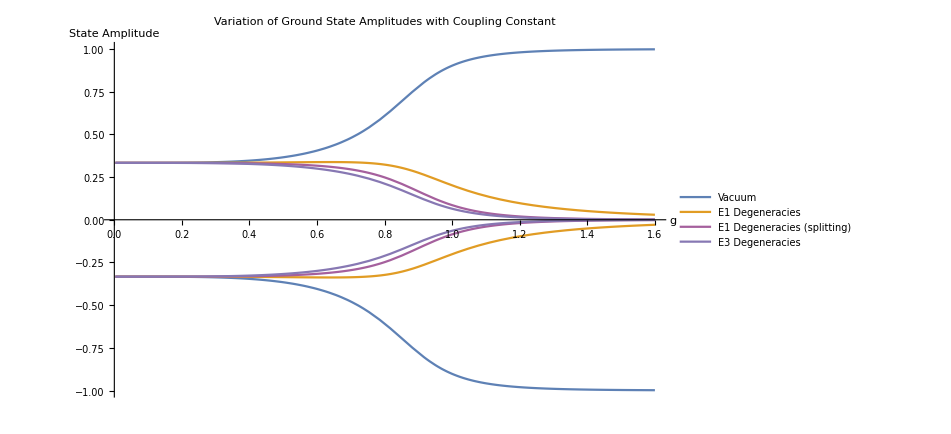

```mathematica
Plot[{Abs[Part[StateN33[g,1,9],1]],Abs[Part[StateN33[g,1,9],5]],Abs[Part[StateN33[g,1,9],2]],Abs[Part[StateN33[g,1,9],8]],-Abs[Part[StateN33[g,1,9],1]],-Abs[Part[StateN33[g,1,9],5]],-Abs[Part[StateN33[g,1,9],2]],-Abs[Part[StateN33[g,1,9],8]]},{g,Sqrt[0.00001],1.6},AxesLabel->{"g","State Amplitude"},PlotLabel->"Variation of Ground State Amplitudes with Coupling Constant",PlotLegends->LineLegend[{"Vacuum","E1 Degeneracies", "E1 Degeneracies (splitting)", "E3 Degeneracies"}],PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5],ColorData[97][1],ColorData[97][2],ColorData[97][9],ColorData[97][5]}]
```

```mathematica
StateN33BasisAmplitude[g_,a_,n_,k_]:=Abs[Part[StateN33[g,a,n],k]]
AverageAmplitude[g_,a_,n_]:=Sum[StateN33BasisAmplitude[g,a,n,k],{k,1,9}]/9
```

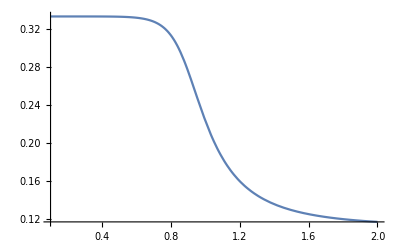

```mathematica
Plot[AverageAmplitude[g,1,9],{g,0.1,2}]
```

```mathematica
AmplitudeVariance[g_,a_,n_]:=Sqrt[Sum[(StateN33BasisAmplitude[g,a,n,k]-AverageAmplitude[g,a,n])^2/9,{k,1,9}]/9]
```

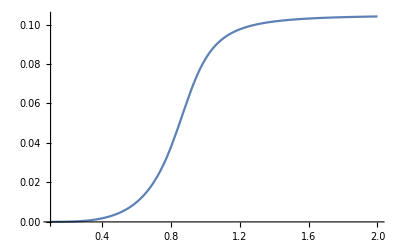

```mathematica
Plot[AmplitudeVariance[g,1,9],{g,0.1,2}]
```

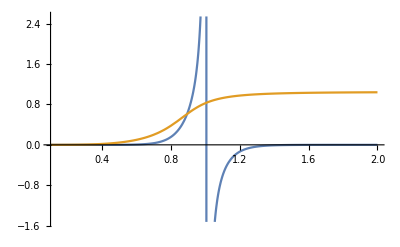

```mathematica
Plot[{EntanglementBeta[g],10AmplitudeVariance[g,1,9]},{g,0.1,2}]
```

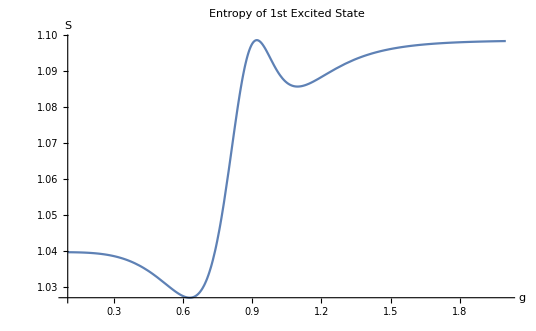

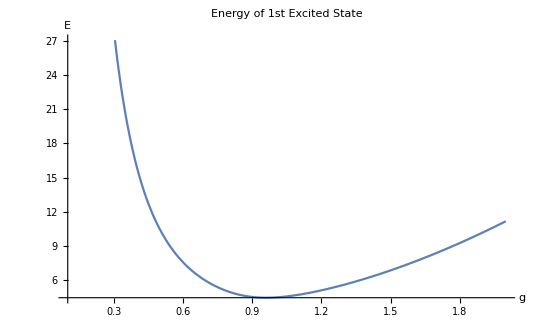

```mathematica
Plot[S33A[g,1,8],{g,0.1,2},PlotLabel->"Entropy of 1st Excited State",AxesLabel->{"g","S"}]
Plot[Part[Eigenvalues[H33[g,1]-500IdentityMatrix[9]],8],{g,0.1,2},PlotLabel->"Energy of 1st Excited State",AxesLabel->{"g","E"}]
```

```mathematica
logisticModel:=a Tanh[b g - c] +
```

```mathematica
parameters:=Join[{a0},Table[b[i],{i,1,39}],Table[c[i],{i,1,39}]]
```

```mathematica
EntropyFunction1E[g_]:=Chop[NonlinearModelFit[EntropyData1E,fourierModel,g,parameters]]
```

```mathematica
FindFit[EntropyData, a Tanh[b g + c]+d,{{a,0.1},{b,-4},{c,3.6},{d,1}},g]
```